```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];(*Get["HopfE`"];*)
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;Format[de]:=δ;Format[eta]:=η;
Format[ga]:=ga;Format[k1]:=Subscript[k,d];Format[k2]:=Subscript[k,g];
Format[muS]:=Subscript[μ,s];Format[laS]:=Subscript[θ,2];Format[th12]:=Subscript[θ,12];
Format[th21]:=Subscript[θ,21];
Format[th]:=θ;Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];
Format[m1]:=Subscript[m,1];Format[m2]:=Subscript[m,2];
Format[mu12]:=Subscript[μ,12];
Format[La]:=Λ;Format[be1]:=Subscript[β,1];(*Format[be2]:=Subscript[β,2];*)
Format[be2]:=Subscript[β,2];Format[be12]:=Subscript[β,12];
```

```mathematica
RN = {0 -> "S", "S" -> 0,
 "S" + "I1"  -> 2*"I1",
 "S" + "I2"  -> 2*"I2",
 "S" + "I12" -> 2*"I12",
 "I1" + "I2" -> "I12",
 "I1" + "I12"-> "I2",
 "I12" -> "I1",
 (*"I12" -> "I2",*)
 "I1" -> 0, "I2" -> 0, "I12" -> 0};
rts={La, muS*S,
 be1*S*I1, 
 be2*S*I2,
 be12*S*I12,
 de*I1*I2,
 eta*I1*I12,
 m1*I12,
(* m2*I12,*)
 mu1*I1, mu2*I2, mu12*I12};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]


{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
Print["siphons are",mSi,"E0 is",E0," R1,R2, ... are",R0A/.E0,"edges=",ed=edgIGMS[RN,mSi]]
jac=Grad[RHS,var];Print["K=",K//MatrixForm,"F=",ng[[2]]//MatrixForm,"V=",ng[[3]]//MatrixForm];
edgIGMS[RN,mSi]
```

reactions and transitions: (0→S | Λ
S→0 | muS S
I1+S→2 I1 | β_1 I1 S
I2+S→2 I2 | β_2 I2 S
I12+S→2 I12 | be12 I12 S
I1+I2→I12 | de I1 I2
I1+I12→I2 | eta I1 I12
I12→I1 | I12 m1
I1→0 | I1 mu1
I2→0 | I2 mu2
I12→0 | I12 mu12)

siphons are{{I1,I12},{I2,I12}}E0 is{S→Λ/muS,I1→0,I12→0,I2→0} R1,R2, ... are{(β_2 Λ)/(mu2 muS),(be12 Λ)/((m1+mu12) muS),(β_1 Λ)/(mu1 muS)}edges={1→2,2→1}

K=((β_1 S)/mu1 | (β_1 m1 S)/(m1 mu1+mu1 mu12) | 0
0 | (be12 S)/(m1+mu12) | 0
0 | 0 | (β_2 S)/mu2)F=(β_1 S | 0 | 0
0 | be12 S | 0
0 | 0 | β_2 S)V=(mu1 | -m1 | 0
0 | m1+mu12 | 0
0 | 0 | mu2)

{1→2,2→1}

```mathematica
(*Module to compute and visualize the IGMS (Infection Graph of Minimal Siphons)*)IGMS[RN_,mSi_]:=Module[{species,infSpecies,igmsEdges,igmsGraph,cycles,n},n=Length[mSi];
(*Extract all species from reaction network*)species=DeleteDuplicates[Flatten[Cases[RN,_String,Infinity]]];
(*Flatten minimal siphons to get all infection species*)infSpecies=DeleteDuplicates[Flatten[mSi]];
Print["Minimal siphons: ",Table[Row[{Subscript["T",i],"=",mSi[[i]]}],{i,n}]];
(*Compute IGMS edges*)igmsEdges=edgIGMS[RN,mSi];
Print["IGMS edges: ",igmsEdges];
(*Create graph*)igmsGraph=Graph[Range[n],igmsEdges,VertexLabels->Table[i->Placed[Row[{Subscript["T",i],"=",Row[mSi[[i]],","]}],Center],{i,n}],VertexSize->0.8,VertexStyle->LightBlue,EdgeStyle->Arrowheads[0.05],VertexLabelStyle->Directive[FontSize->14,Bold],GraphLayout->"SpringElectricalEmbedding",ImageSize->Large];
(*Find cycles*)cycles=FindCycle[igmsGraph,Infinity,All];
If[Length[cycles]>0,Print["Cycles in IGMS (",Length[cycles]," found): "];
Do[Print["  Cycle ",i,": ",cycles[[i]]],{i,Length[cycles]}],Print["IGMS is acyclic (no cycles found)"]];
(*Return association with all computed data*)<|"MinimalSiphons"->mSi,"IGMSEdges"->igmsEdges,"IGMSGraph"->igmsGraph,"Cycles"->cycles,"IsAcyclic"->(Length[cycles]==0)|>]

(*Compute edges of IGMS graph*)
edgIGMS[RN_,mSi_]:=Module[{n,igmsEdges},n=Length[mSi];
igmsEdges={};
Do[Do[If[i!=j,Do[If[canActRea[reaction,mSi[[i]],mSi[[j]]],AppendTo[igmsEdges,i->j];
Break[]],{reaction,RN}]],{j,n}],{i,n}];
igmsEdges]

(*Helper:Check if one reaction activates Sj from Si*)
canActRea[reaction_,Si_,Sj_]:=Module[{lhs,rhs,lhsSpecies,rhsSpecies,newSpecies,netProduction,SiStr,SjStr},(*Convert Si and Sj to strings if they're symbols*)SiStr=ToString/@Si;
SjStr=ToString/@Sj;
(*Skip birth and death reactions*)If[reaction===(0->_)||reaction===(_->0),Return[False]];
lhs=reaction[[1]];
rhs=reaction[[2]];
(*Extract species*)lhsSpecies=Cases[{lhs},_String,Infinity];
rhsSpecies=Cases[{rhs},_String,Infinity];
(*Quick filter:skip if reaction doesn't involve infection species*)If[Length[Intersection[lhsSpecies,SiStr]]==0,Return[False]];
(*Find species that need to be produced*)newSpecies=Complement[SjStr,SiStr];
If[Length[newSpecies]==0,Return[False]];
(*Check net production*)netProduction=Table[Count[rhsSpecies,sp]-Count[lhsSpecies,sp],{sp,newSpecies}];
Max[netProduction]>0]

$DebugIGMS=False;

(*Example usage:*)
(*RN={0->"S","S"->0,"S"+"I1"->2*"I1","S"+"I2"->2*"I2","I1"+"I2"->"I12","I1"+"I12"->"I2","I2"+"I12"->"I1","I1"->0,"I2"->0,"I12"->0};
mSi={{"I1","I2"},{"I2","I12"},{"I1","I12"}};
result=IGMS[RN,mSi];
result["IGMSGraph"]*)
```

{}

True

Minimal siphons: {T_1={I1,I2}}

IGMS edges: {}

IGMS is acyclic (no cycles found)

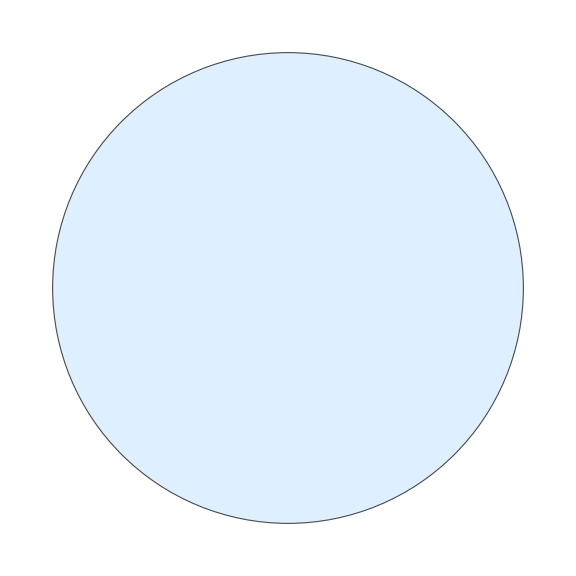
<|MinimalSiphons→{{I1,I2}},IGMSEdges→{},IGMSGraph→-Graphics-,Cycles→{},IsAcyclic→True|>

```mathematica
edgIGMS[RN, mSi]
$DebugIGMS=True
result = IGMS[RN, mSi]
```

```mathematica
(*Test edgIGMS*)(*Copy canActRea here for standalone testing*)canActRea[reaction_,Si_,Sj_]:=Module[{lhs,rhs,lhsSpecies,rhsSpecies,newSpecies,netProduction},(*Skip birth and death reactions*)If[reaction===(0->_)||reaction===(_->0),Return[False]];
lhs=reaction[[1]];
rhs=reaction[[2]];
(*Extract species*)lhsSpecies=Cases[{lhs},_String,Infinity];
rhsSpecies=Cases[{rhs},_String,Infinity];
(*Quick filter:skip if reaction doesn't involve infection species*)If[Length[Intersection[lhsSpecies,Si]]==0,Return[False]];
(*Find species that need to be produced*)newSpecies=Complement[Sj,Si];
If[Length[newSpecies]==0,Return[False]];
(*Check net production*)netProduction=Table[Count[rhsSpecies,sp]-Count[lhsSpecies,sp],{sp,newSpecies}];
Max[netProduction]>0]

(*Copy edgIGMS here*)
edgIGMS[RN_,mSi_]:=Module[{n,igmsEdges},n=Length[mSi];
Print["Testing edgIGMS with ",n," siphons"];
Print["RN has ",Length[RN]," reactions"];
igmsEdges={};
Do[Do[If[i!=j,Print["  Checking T",i,"=",mSi[[i]]," -> T",j,"=",mSi[[j]]];
Do[If[canActRea[reaction,mSi[[i]],mSi[[j]]],Print["    Found activation via: ",reaction];
AppendTo[igmsEdges,i->j];
Break[]],{reaction,RN}]],{j,n}],{i,n}];
igmsEdges]

(*Test data*)
RN={0->"S","S"->0,"S"+"I1"->2*"I1","S"+"I2"->2*"I2","I1"+"I2"->"I12","I1"+"I12"->"I2","I2"+"I12"->"I1","I1"->0,"I2"->0,"I12"->0};

mSi={{"I1","I2"},{"I2","I12"},{"I1","I12"}};

(*Run test*)
Print["=== Testing edgIGMS ==="];
edges=edgIGMS[RN,mSi]
Print["Result: ",edges];
```

=== Testing edgIGMS ===

Testing edgIGMS with 3 siphons

RN has 10 reactions

Checking T1={I1,I2} -> T2={I2,I12}

Found activation via: I1+I2→I12

Checking T1={I1,I2} -> T3={I1,I12}

Found activation via: I1+I2→I12

Checking T2={I2,I12} -> T1={I1,I2}

Found activation via: I12+I2→I1

Checking T2={I2,I12} -> T3={I1,I12}

Found activation via: I12+I2→I1

Checking T3={I1,I12} -> T1={I1,I2}

Found activation via: I1+I12→I2

Checking T3={I1,I12} -> T2={I2,I12}

Found activation via: I1+I12→I2

{1→2,1→3,2→1,2→3,3→1,3→2}

Result: {1→2,1→3,2→1,2→3,3→1,3→2}

```mathematica
(*E1*)
cE1=bdfp[[2]][[1]][[1]];po2=Collect[bdfp[[1]][[2]]/i2,i2];
{R12,R21,coP}=invN[cE1,F,R0A,E0,par,cp];
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff R12 <1"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

reactions and transitions: (0→S | muS
S→0 | muS S
I1+S→2 I1 | beta1 I1 S
I2+S→2 I2 | beta2 I2 S
I12+S→2 I12 | beta12 I12 S
I12→I1 | I12 m21
I12→I2 | I12 m2
I1+I2→I12 | delta I1 I2
I1→0 | I1 mu1
I2→0 | I2 mu2
I12→0 | I12 mu12)

```mathematica
{muS-beta1 I1 S-be12 I3 S-be2 I2 S-muS S,-delta I1 I2+I3 m1-I1 mu1+beta1 I1 S,-delta I1 I2+I3 m2-I2 mu2+be2 I2 S,delta I1 I2-I3 m2-I3 m1-I3 mu12+be12 I3 S}
```

siphons are{{I1,I12},{I2,I12}}E0 is{S→1,I1→0,I12→0,I2→0} R1,R2 are{beta2/mu2,beta12/(m2+m21+mu12),beta1/mu1}

fps on siphon facet {I1,I12}: 2 boundary points

fps on siphon facet {I2,I12}: 2 boundary points

```mathematica
{{{{I2->0,S->1},{I2->((be2-mu2) muS)/(be2 mu2),S->mu2/be2}},EpidCRN`Private`AllSolsRational},{{{I1->0,S->1},{I1->((beta1-mu1) muS)/(beta1 mu1),S->mu1/beta1}},EpidCRN`Private`AllSolsRational}}
```

R0A has 3 elements

Invasion numbers: R12 = beta12/(m2+m21+mu12), R21 = nonRat

At least one equilibrium irrational - coexistence analysis not possible

At cE1, chp of jac, ch1, factorizes as

```mathematica
(*EE*)
eq=Thread[RHS==0];so=Solve[eq,var];
Print["There are ",so//Length," fps "]
cEE=so[[2]]//FullSimplify
Print["Existence of EE holds iff R1>R2,  R12 <1, R21<1"]
reE=Reduce[Join[cp,Thread[(var/.cEE)>=0]]]//FullSimplify
jE=jac/.cEE//FullSimplify;
Print[" At cEE, chp of jac, chE, factorizes as"]
chE=Numerator[Together[CharacteristicPolynomial[jE,u]]]//Factor
```

There are 5 fps

{s→μ_1/β_1,i_1→Λ/μ_1+(-μ+(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(β_2 μ_1-β_1 μ_2),i_2→-μ_v/β_v+(μ_1 ρ)/(-β_2 μ_1+β_1 μ_2),v→(-β_2 μ_1+β_1 μ_2)/(β_1 β_v)}

Existence of EE holds iff R1>R2,  R12 <1, R21<1

μ_2>0&&μ_1>0&&β_2>0&&β_1>(β_2 μ_1)/μ_2&&ρ>0&&μ_v>0&&β_v≥(-β_2 μ_1 μ_v+β_1 μ_2 μ_v)/(μ_1 ρ)&&μ>0&&Λ≥μ_1 ((μ-(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(-β_2 μ_1+β_1 μ_2))

At cEE, chp of jac, chE, factorizes as

β_1 β_2^3 β_v Λ μ_1^4 μ_v-β_2^3 β_v μ μ_1^5 μ_v-3 β_1^2 β_2^2 β_v Λ μ_1^3 μ_2 μ_v+3 β_1 β_2^2 β_v μ μ_1^4 μ_2 μ_v+3 β_1^3 β_2 β_v Λ μ_1^2 μ_2^2 μ_v-3 β_1^2 β_2 β_v μ μ_1^3 μ_2^2 μ_v-β_1^4 β_v Λ μ_1 μ_2^3 μ_v+β_1^3 β_v μ μ_1^2 μ_2^3 μ_v+β_2^4 μ_1^5 μ_v^2-3 β_1 β_2^3 μ_1^4 μ_2 μ_v^2+3 β_1^2 β_2^2 μ_1^3 μ_2^2 μ_v^2-β_1^3 β_2 μ_1^2 μ_2^3 μ_v^2+β_1 β_2^2 β_v^2 Λ μ_1^4 ρ-β_2^2 β_v^2 μ μ_1^5 ρ-2 β_1^2 β_2 β_v^2 Λ μ_1^3 μ_2 ρ+2 β_1 β_2 β_v^2 μ μ_1^4 μ_2 ρ+β_1^3 β_v^2 Λ μ_1^2 μ_2^2 ρ-β_1^2 β_v^2 μ μ_1^3 μ_2^2 ρ+β_2^3 β_v μ_1^5 μ_v ρ-β_1 β_2^2 β_v μ_1^4 μ_2 μ_v ρ-β_1^2 β_2 β_v μ_1^3 μ_2^2 μ_v ρ+β_1^3 β_v μ_1^2 μ_2^3 μ_v ρ+β_1 β_2 β_v^2 μ_1^4 μ_2 ρ^2-β_1^2 β_v^2 μ_1^3 μ_2^2 ρ^2+β_1 β_2^3 β_v Λ μ_1^3 μ_v u-3 β_1^2 β_2^2 β_v Λ μ_1^2 μ_2 μ_v u+3 β_1^3 β_2 β_v Λ μ_1 μ_2^2 μ_v u-β_1^4 β_v Λ μ_2^3 μ_v u-β_1^2 β_2 β_v^2 Λ μ_1^3 ρ u+β_1 β_2^2 β_v^2 Λ μ_1^3 ρ u+β_1 β_2 β_v^2 μ μ_1^4 ρ u+β_1^3 β_v^2 Λ μ_1^2 μ_2 ρ u-2 β_1^2 β_2 β_v^2 Λ μ_1^2 μ_2 ρ u-β_1^2 β_v^2 μ μ_1^3 μ_2 ρ u+β_1^3 β_v^2 Λ μ_1 μ_2^2 ρ u-β_1 β_2^2 β_v μ_1^4 μ_v ρ u+β_1^2 β_2 β_v μ_1^3 μ_2 μ_v ρ u+β_1 β_2^2 β_v μ_1^3 μ_2 μ_v ρ u-β_1^2 β_2 β_v μ_1^2 μ_2^2 μ_v ρ u-β_1^2 β_v^2 μ_1^3 μ_2 ρ^2 u+β_1 β_2 β_v^2 μ_1^3 μ_2 ρ^2 u+β_1^2 β_2^2 β_v Λ μ_1^3 u^2-β_1 β_2^2 β_v μ μ_1^4 u^2-2 β_1^3 β_2 β_v Λ μ_1^2 μ_2 u^2+2 β_1^2 β_2 β_v μ μ_1^3 μ_2 u^2+β_1^4 β_v Λ μ_1 μ_2^2 u^2-β_1^3 β_v μ μ_1^2 μ_2^2 u^2+β_1 β_2^3 μ_1^4 μ_v u^2-β_2^4 μ_1^4 μ_v u^2+β_2^3 β_v μ_1^4 μ_v u^2-2 β_1^2 β_2^2 μ_1^3 μ_2 μ_v u^2+2 β_1 β_2^3 μ_1^3 μ_2 μ_v u^2-3 β_1 β_2^2 β_v μ_1^3 μ_2 μ_v u^2+β_1^3 β_2 μ_1^2 μ_2^2 μ_v u^2-β_1^2 β_2^2 μ_1^2 μ_2^2 μ_v u^2+3 β_1^2 β_2 β_v μ_1^2 μ_2^2 μ_v u^2-β_1^3 β_v μ_1 μ_2^3 μ_v u^2-β_1^2 β_2 β_v^2 Λ μ_1^2 ρ u^2-β_2^3 β_v μ_1^4 ρ u^2+β_2^2 β_v^2 μ_1^4 ρ u^2+β_1^3 β_v^2 Λ μ_1 μ_2 ρ u^2+β_1^2 β_2 β_v μ_1^3 μ_2 ρ u^2+β_1 β_2^2 β_v μ_1^3 μ_2 ρ u^2-2 β_1 β_2 β_v^2 μ_1^3 μ_2 ρ u^2-β_1^3 β_v μ_1^2 μ_2^2 ρ u^2+β_1^2 β_v^2 μ_1^2 μ_2^2 ρ u^2+β_1^2 β_2^2 β_v Λ μ_1^2 u^3-2 β_1^3 β_2 β_v Λ μ_1 μ_2 u^3+β_1^4 β_v Λ μ_2^2 u^3-β_1 β_2 β_v^2 μ_1^3 ρ u^3+β_1^2 β_v^2 μ_1^2 μ_2 ρ u^3+β_1 β_2^2 β_v μ_1^3 u^4-2 β_1^2 β_2 β_v μ_1^2 μ_2 u^4+β_1^3 β_v μ_1 μ_2^2 u^4

```mathematica
(*E2*)c1=Thread[mSi[[1]]->0];
RH2=remZ[RHS/.c1//FullSimplify];RH2[[2]]=(RHS/.c1)[[3]]/i2//Factor
RH2
so=Solve[Thread[RH2[[{1,3}]]==0],{s,v}]//Flatten
co=FullSimplify/@CoefficientList[po2,i2]
pc=co[[1]]<0||(co[[1]]>=0&&co[[2]]^2-4 co[[1]]*co[[3]]<0);
(*re=Reduce[Append[cp,co[[1]]<=0]]//FullSimplify
re=Reduce[Append[cp,pc]]//FullSimplify ; funny answers*)
```

-μ_2+β_2 s+β_v v

{Λ-(β_2 i_2+μ+ρ) s,-μ_2+β_2 s+β_v v,ρ s-(β_v i_2+μ_v) v}

{s→Λ/(β_2 i_2+μ+ρ),v→(Λ ρ)/((β_v i_2+μ_v) (β_2 i_2+μ+ρ))}

{-β_2 Λ μ_v-β_v Λ ρ+μ_2 μ_v (μ+ρ),β_2 (-β_v Λ+μ_2 μ_v)+β_v μ_2 (μ+ρ),β_2 β_v μ_2}

```mathematica
j2=jac/.so/.i1->0//FullSimplify;
Print[" At cE2, chp of jac, ch2, factorizes as"]
ch2=Numerator[Together[CharacteristicPolynomial[j2,u]]]//Factor
List@@ch2//Length
{lSta,qSta,hDeg,ll,ql}=sta[ch2]
```

At cE2, chp of jac, ch2, factorizes as

(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2-2 β_2 i_2 μ μ_2 μ_v^2-μ^2 μ_2 μ_v^2-2 β_2 β_v^2 i_2^3 μ_2 ρ-2 β_v^2 i_2^2 μ μ_2 ρ+2 β_2 β_v i_2 Λ μ_v ρ+β_v Λ μ μ_v ρ-4 β_2 β_v i_2^2 μ_2 μ_v ρ-4 β_v i_2 μ μ_2 μ_v ρ+β_2 Λ μ_v^2 ρ-2 β_2 i_2 μ_2 μ_v^2 ρ-2 μ μ_2 μ_v^2 ρ-β_v^2 i_2^2 μ_2 ρ^2+β_v Λ μ_v ρ^2-2 β_v i_2 μ_2 μ_v ρ^2-μ_2 μ_v^2 ρ^2-β_2^2 β_v^2 i_2^4 u+β_2 β_v^2 i_2^2 Λ u-2 β_2 β_v^2 i_2^3 μ u+β_2 β_v i_2 Λ μ u-β_v^2 i_2^2 μ^2 u-β_2^2 β_v i_2^3 μ_2 u-β_2 β_v^2 i_2^3 μ_2 u-2 β_2 β_v i_2^2 μ μ_2 u-β_v^2 i_2^2 μ μ_2 u-β_v i_2 μ^2 μ_2 u-2 β_2^2 β_v i_2^3 μ_v u+2 β_2 β_v i_2 Λ μ_v u-4 β_2 β_v i_2^2 μ μ_v u+β_2 Λ μ μ_v u-2 β_v i_2 μ^2 μ_v u-β_2^2 i_2^2 μ_2 μ_v u-2 β_2 β_v i_2^2 μ_2 μ_v u-2 β_2 i_2 μ μ_2 μ_v u-2 β_v i_2 μ μ_2 μ_v u-μ^2 μ_2 μ_v u-β_2^2 i_2^2 μ_v^2 u+β_2 Λ μ_v^2 u-2 β_2 i_2 μ μ_v^2 u-μ^2 μ_v^2 u-β_2 i_2 μ_2 μ_v^2 u-μ μ_2 μ_v^2 u-2 β_2 β_v^2 i_2^3 ρ u+2 β_2 β_v i_2 Λ ρ u-2 β_v^2 i_2^2 μ ρ u+β_v Λ μ ρ u-2 β_2 β_v i_2^2 μ_2 ρ u-β_v^2 i_2^2 μ_2 ρ u-2 β_v i_2 μ μ_2 ρ u-4 β_2 β_v i_2^2 μ_v ρ u+β_2 Λ μ_v ρ u+β_v Λ μ_v ρ u-4 β_v i_2 μ μ_v ρ u-2 β_2 i_2 μ_2 μ_v ρ u-2 β_v i_2 μ_2 μ_v ρ u-2 μ μ_2 μ_v ρ u-2 β_2 i_2 μ_v^2 ρ u-2 μ μ_v^2 ρ u-μ_2 μ_v^2 ρ u-β_v^2 i_2^2 ρ^2 u+β_v Λ ρ^2 u-β_v i_2 μ_2 ρ^2 u-2 β_v i_2 μ_v ρ^2 u-μ_2 μ_v ρ^2 u-μ_v^2 ρ^2 u-β_2^2 β_v i_2^3 u^2-β_2 β_v^2 i_2^3 u^2+β_2 β_v i_2 Λ u^2-2 β_2 β_v i_2^2 μ u^2-β_v^2 i_2^2 μ u^2-β_v i_2 μ^2 u^2-β_2 β_v i_2^2 μ_2 u^2-β_v i_2 μ μ_2 u^2-β_2^2 i_2^2 μ_v u^2-2 β_2 β_v i_2^2 μ_v u^2+β_2 Λ μ_v u^2-2 β_2 i_2 μ μ_v u^2-2 β_v i_2 μ μ_v u^2-μ^2 μ_v u^2-β_2 i_2 μ_2 μ_v u^2-μ μ_2 μ_v u^2-β_2 i_2 μ_v^2 u^2-μ μ_v^2 u^2-2 β_2 β_v i_2^2 ρ u^2-β_v^2 i_2^2 ρ u^2+β_v Λ ρ u^2-2 β_v i_2 μ ρ u^2-β_v i_2 μ_2 ρ u^2-2 β_2 i_2 μ_v ρ u^2-2 β_v i_2 μ_v ρ u^2-2 μ μ_v ρ u^2-μ_2 μ_v ρ u^2-μ_v^2 ρ u^2-β_v i_2 ρ^2 u^2-μ_v ρ^2 u^2-β_2 β_v i_2^2 u^3-β_v i_2 μ u^3-β_2 i_2 μ_v u^3-μ μ_v u^3-β_v i_2 ρ u^3-μ_v ρ u^3)

2

Set::shape: Lists {lSta,qSta,hDeg,ll,ql} and sta[(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2+«100»)] are not the same shape.

sta[(β_1 Λ-β_2 i_2 μ_1-μ μ_1-μ_1 ρ-β_2 i_2 u-μ u-ρ u) (β_2 β_v^2 i_2^2 Λ μ-β_2^2 β_v^2 i_2^4 μ_2-2 β_2 β_v^2 i_2^3 μ μ_2-β_v^2 i_2^2 μ^2 μ_2+2 β_2 β_v i_2 Λ μ μ_v-2 β_2^2 β_v i_2^3 μ_2 μ_v-4 β_2 β_v i_2^2 μ μ_2 μ_v-2 β_v i_2 μ^2 μ_2 μ_v+β_2 Λ μ μ_v^2-β_2^2 i_2^2 μ_2 μ_v^2-2 β_2 i_2 μ μ_2 μ_v^2-μ^2 μ_2 μ_v^2-2 β_2 β_v^2 i_2^3 μ_2 ρ-2 β_v^2 i_2^2 μ μ_2 ρ+2 β_2 β_v i_2 Λ μ_v ρ+β_v Λ μ μ_v ρ-4 β_2 β_v i_2^2 μ_2 μ_v ρ-4 β_v i_2 μ μ_2 μ_v ρ+β_2 Λ μ_v^2 ρ-2 β_2 i_2 μ_2 μ_v^2 ρ-2 μ μ_2 μ_v^2 ρ-β_v^2 i_2^2 μ_2 ρ^2+β_v Λ μ_v ρ^2-2 β_v i_2 μ_2 μ_v ρ^2-μ_2 μ_v^2 ρ^2-β_2^2 β_v^2 i_2^4 u+β_2 β_v^2 i_2^2 Λ u-2 β_2 β_v^2 i_2^3 μ u+β_2 β_v i_2 Λ μ u-β_v^2 i_2^2 μ^2 u-β_2^2 β_v i_2^3 μ_2 u-β_2 β_v^2 i_2^3 μ_2 u-2 β_2 β_v i_2^2 μ μ_2 u-β_v^2 i_2^2 μ μ_2 u-β_v i_2 μ^2 μ_2 u-2 β_2^2 β_v i_2^3 μ_v u+2 β_2 β_v i_2 Λ μ_v u-4 β_2 β_v i_2^2 μ μ_v u+β_2 Λ μ μ_v u-2 β_v i_2 μ^2 μ_v u-β_2^2 i_2^2 μ_2 μ_v u-2 β_2 β_v i_2^2 μ_2 μ_v u-2 β_2 i_2 μ μ_2 μ_v u-2 β_v i_2 μ μ_2 μ_v u-μ^2 μ_2 μ_v u-β_2^2 i_2^2 μ_v^2 u+β_2 Λ μ_v^2 u-2 β_2 i_2 μ μ_v^2 u-μ^2 μ_v^2 u-β_2 i_2 μ_2 μ_v^2 u-μ μ_2 μ_v^2 u-2 β_2 β_v^2 i_2^3 ρ u+2 β_2 β_v i_2 Λ ρ u-2 β_v^2 i_2^2 μ ρ u+β_v Λ μ ρ u-2 β_2 β_v i_2^2 μ_2 ρ u-β_v^2 i_2^2 μ_2 ρ u-2 β_v i_2 μ μ_2 ρ u-4 β_2 β_v i_2^2 μ_v ρ u+β_2 Λ μ_v ρ u+β_v Λ μ_v ρ u-4 β_v i_2 μ μ_v ρ u-2 β_2 i_2 μ_2 μ_v ρ u-2 β_v i_2 μ_2 μ_v ρ u-2 μ μ_2 μ_v ρ u-2 β_2 i_2 μ_v^2 ρ u-2 μ μ_v^2 ρ u-μ_2 μ_v^2 ρ u-β_v^2 i_2^2 ρ^2 u+β_v Λ ρ^2 u-β_v i_2 μ_2 ρ^2 u-2 β_v i_2 μ_v ρ^2 u-μ_2 μ_v ρ^2 u-μ_v^2 ρ^2 u-β_2^2 β_v i_2^3 u^2-β_2 β_v^2 i_2^3 u^2+β_2 β_v i_2 Λ u^2-2 β_2 β_v i_2^2 μ u^2-β_v^2 i_2^2 μ u^2-β_v i_2 μ^2 u^2-β_2 β_v i_2^2 μ_2 u^2-β_v i_2 μ μ_2 u^2-β_2^2 i_2^2 μ_v u^2-2 β_2 β_v i_2^2 μ_v u^2+β_2 Λ μ_v u^2-2 β_2 i_2 μ μ_v u^2-2 β_v i_2 μ μ_v u^2-μ^2 μ_v u^2-β_2 i_2 μ_2 μ_v u^2-μ μ_2 μ_v u^2-β_2 i_2 μ_v^2 u^2-μ μ_v^2 u^2-2 β_2 β_v i_2^2 ρ u^2-β_v^2 i_2^2 ρ u^2+β_v Λ ρ u^2-2 β_v i_2 μ ρ u^2-β_v i_2 μ_2 ρ u^2-2 β_2 i_2 μ_v ρ u^2-2 β_v i_2 μ_v ρ u^2-2 μ μ_v ρ u^2-μ_2 μ_v ρ u^2-μ_v^2 ρ u^2-β_v i_2 ρ^2 u^2-μ_v ρ^2 u^2-β_2 β_v i_2^2 u^3-β_v i_2 μ u^3-β_2 i_2 μ_v u^3-μ μ_v u^3-β_v i_2 ρ u^3-μ_v ρ u^3)]

```mathematica
re=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

ρ>0&&μ>0&&μ_1>0&&Λ>0&&μ_v>0&&μ_2>0&&β_v>0&&β_2>0&&μ_1 (μ+ρ)<β_1 Λ&&β_2 μ_1 μ_v+β_v μ_1 ρ<β_1 μ_2 μ_v

```mathematica
j1=jac/.cE1/.i2->0//FullSimplify;
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]]]//Factor
Apart/@SolveValues[ch1==0,u]
{lSta,qSta,hDeg,ll,ql}=sta[ch1]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify
```

There are 5 fps

{s→μ_1/β_1,i_1→Λ/μ_1+(-μ+(β_2 μ_v)/β_v)/β_1+(μ_2 ρ)/(β_2 μ_1-β_1 μ_2),i_2→-μ_v/β_v+(μ_1 ρ)/(-β_2 μ_1+β_1 μ_2),v→(-β_2 μ_1+β_1 μ_2)/(β_1 β_v)}

```mathematica
so4=so[[4]]//FullSimplify
```

{s→(β_2 (-β_v Λ+μ_2 μ_v)-β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 (-β_v μ+β_2 μ_v)),i_1→0,i_2→(β_2 (β_v Λ-μ_2 μ_v)-β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 β_v μ_2),v→(-β_2 (β_v Λ+μ_2 μ_v)+β_v μ_2 (μ-ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_v (β_v μ-β_2 μ_v))}

```mathematica
so5=so[[5]]//FullSimplify
```

{s→(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ)+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 (β_v μ-β_2 μ_v)),i_1→0,i_2→-(-β_2 β_v Λ+β_v μ μ_2+β_2 μ_2 μ_v+β_v μ_2 ρ+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_2 β_v μ_2),v→-(β_2 β_v Λ-β_v μ μ_2+β_2 μ_2 μ_v+β_v μ_2 ρ+√(4 β_2 β_v Λ μ_2 (-β_v μ+β_2 μ_v)+(β_2 (β_v Λ-μ_2 μ_v)+β_v μ_2 (μ+ρ))^2))/(2 β_v (β_v μ-β_2 μ_v))}

Checked 513 potential coexistence points

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

All Rij equations: {0.36499 β_1==1,0.523457 (1.6307+0.652971 β_2)==1,(1.07109 (2.18349+0.874319 β_2))/β_1==1,-(0.319659 β_1 (8.37744+1.19315 β_2-√((-8.37744-1.19315 β_2)^2-21.8809 (2.20175 β_2-0.874319 β_2^2))))/((-2.51824+β_2) β_2)==1}

DFE: 140 (2%)

E2: 2369 (40%)

E1: 2937 (49%)

EE-Stable: 513 (9%)

{11.5313,Null}

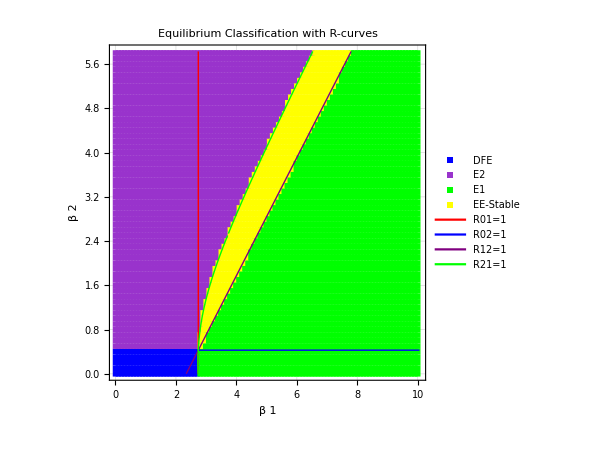

```mathematica
plotInd={1,2};varInd={1,2,3};p0val=par/.coP;steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[{fPl,unC,res}=scan[RHS,var,par,p0val,plotInd,varInd,Automatic,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]
fPl
```

```mathematica
Export["LiScan.pdf",fPl]
```

LiScan.pdf

```mathematica
(*Test CanActivate for a single reaction*)(*CanActivate for a single reaction:Does reaction r activate Sj when Si is active?*)CanActivateReaction[reaction_,Si_,Sj_]:=Module[{lhs,rhs,lhsSpecies,rhsSpecies,hasInfectedReactant,newSpecies,netProduction},(*Skip birth and death reactions*)If[reaction===(0->_)||reaction===(_->0),Return[False]];
lhs=reaction[[1]];
rhs=reaction[[2]];
(*Extract species from left and right hand sides*)lhsSpecies=Cases[{lhs},_String,Infinity];
rhsSpecies=Cases[{rhs},_String,Infinity];
Print["Reaction: ",reaction];
Print["  LHS species: ",lhsSpecies];
Print["  RHS species: ",rhsSpecies];
(*Check if an infected individual from Si is a reactant*)hasInfectedReactant=Length[Intersection[lhsSpecies,Si]]>0;
Print["  Has infected reactant from Si=",Si,": ",hasInfectedReactant];
(*Find species that are in Sj but not in Si*)newSpecies=Complement[Sj,Si];
Print["  New species (in Sj but not Si): ",newSpecies];
If[!hasInfectedReactant||Length[newSpecies]==0,Print["  -> NO ACTIVATION"];
Return[False]];
(*Check net production of species in newSpecies*)netProduction=Table[Count[rhsSpecies,sp]-Count[lhsSpecies,sp],{sp,newSpecies}];
Print["  Net production of new species: ",netProduction];
If[Max[netProduction]>0,Print["  -> ACTIVATION! Produces ",newSpecies[[Position[netProduction,Max[netProduction]][[1,1]]]]];
True,Print["  -> NO ACTIVATION"];
False]]

(*Test cases*)
Print["=== Test 1: I1+I2->I12 with Si={I1,I2}, Sj={I2,I12} ==="];
CanActivateReaction["I1"+"I2"->"I12",{"I1","I2"},{"I2","I12"}]

Print["\n=== Test 2: I1+I12->I2 with Si={I1,I12}, Sj={I1,I2} ==="];
CanActivateReaction["I1"+"I12"->"I2",{"I1","I12"},{"I1","I2"}]

Print["\n=== Test 3: I2+I12->I1 with Si={I2,I12}, Sj={I1,I2} ==="];
CanActivateReaction["I2"+"I12"->"I1",{"I2","I12"},{"I1","I2"}]

Print["\n=== Test 4: S+I1->2*I1 with Si={I1,I2}, Sj={I2,I12} ==="];
CanActivateReaction["S"+"I1"->2*"I1",{"I1","I2"},{"I2","I12"}]
```

=== Test 1: I1+I2->I12 with Si={I1,I2}, Sj={I2,I12} ===

Reaction: I1+I2→I12

LHS species: {I1,I2}

RHS species: {I12}

Has infected reactant from Si={I1,I2}: True

New species (in Sj but not Si): {I12}

Net production of new species: {1}

-> ACTIVATION! Produces I12

True

=== Test 2: I1+I12->I2 with Si={I1,I12}, Sj={I1,I2} ===

Reaction: I1+I12→I2

LHS species: {I1,I12}

RHS species: {I2}

Has infected reactant from Si={I1,I12}: True

New species (in Sj but not Si): {I2}

Net production of new species: {1}

-> ACTIVATION! Produces I2

True

=== Test 3: I2+I12->I1 with Si={I2,I12}, Sj={I1,I2} ===

Reaction: I12+I2→I1

LHS species: {I12,I2}

RHS species: {I1}

Has infected reactant from Si={I2,I12}: True

New species (in Sj but not Si): {I1}

Net production of new species: {1}

-> ACTIVATION! Produces I1

True

=== Test 4: S+I1->2*I1 with Si={I1,I2}, Sj={I2,I12} ===

Reaction: I1+S→2 I1

LHS species: {I1,S}

RHS species: {I1}

Has infected reactant from Si={I1,I2}: True

New species (in Sj but not Si): {I12}

Net production of new species: {0}

-> NO ACTIVATION

False